# Analysis of data obtained with VASP

Milagros Delgado^1, Jhon Aponte^2, Matías Romero^2, Rolando Sánchez^1, and Andrés Toledo^1
[1] School of Physical Sciences and Nanotechnology, Yachay Tech University, Urcuquí - Ecuador
[2] School of Chemical Sciences and Engineering,  Yachay Tech University, Urcuquí - Ecuador

## Al

```mathematica
wrk = "/home/rolando/Downloads/Yachay/8th_Semester/dft/dft_coursework/midterm/MidTerm Challenge proyect/al-files/results";
SetDirectory[wrk];
```

### Analysis of ENCUT

```mathematica
datasi = Import["ecut.dat"]//Map[#/{1,2}&,#]&;
datasi//TableForm
```

250 | -1.88524
300 | -1.88778
350 | -1.8892
400 | -1.88953
450 | -1.88971
500 | -1.88973
550 | -1.88975
600 | -1.88977
650 | -1.8898
700 | -1.88982
750 | -1.88982
800 | -1.88983
850 | -1.88983
900 | -1.88984

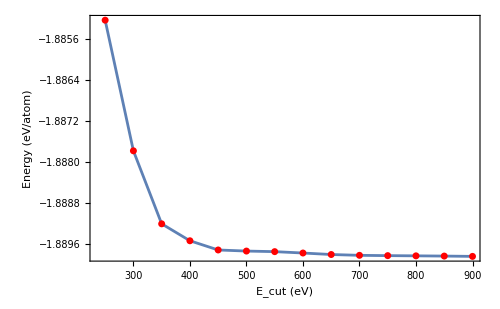

```mathematica
datasi //ListPlot[#,
Frame ->True,
FrameLabel->{"E_cut (eV)", "Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->500,
Epilog->{Red, AbsolutePointSize[5], Point[#]}
]&
```

Let our convergence criteria to be 1 meV/atom

Using the criteria, let’s obtain a convergence window to find the E_cut

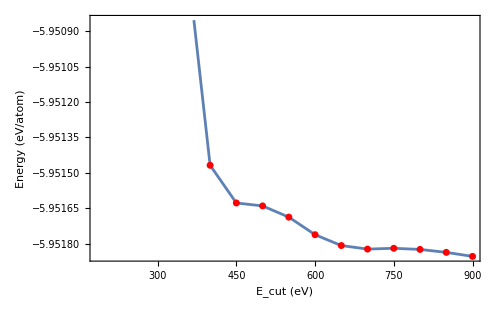

```mathematica
datasi //ListPlot[#,
Frame ->True,
FrameLabel->{"E_cut (eV)", "Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->15},
Joined->True,
PlotRange->{#[[-1,2]],#[[-1,2] ]+10^-3},
InterpolationOrder->1,
ImageSize->500,
Epilog->{Red, AbsolutePointSize[5], Point[#]}
]&
```

### Analysis of k-points

```mathematica
datakp = Import["kps.dat"]//Map[#/{1,2}&,#]&;
datakp//TableForm
```

3 | -5.63543
4 | -5.85444
5 | -5.91801
6 | -5.93916
7 | -5.94678
8 | -5.94976
9 | -5.95096
10 | -5.95151
11 | -5.9517
12 | -5.95181

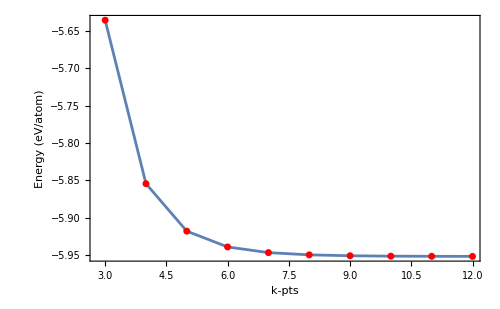

```mathematica
datakp //ListPlot[#,
Frame ->True,
FrameLabel->{"k-pts", "Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->500,
Epilog->{Red, AbsolutePointSize[5], Point[#]}
]&
```

Let' s obtain a convergence window to find the optimal kpoints .

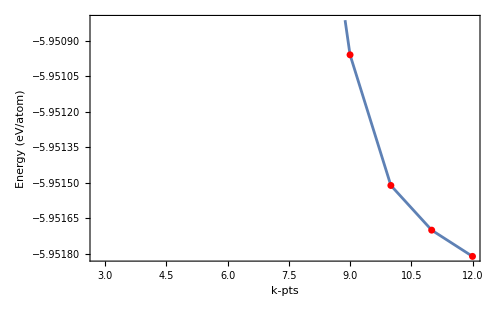

```mathematica
datakp //ListPlot[#,
Frame ->True,
FrameLabel->{"k-pts", "Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->15},
Joined->True,
PlotRange->{#[[-1,2]],#[[-1,2] ]+10^-3},
InterpolationOrder->1,
ImageSize->500,
Epilog->{Red, AbsolutePointSize[5], Point[#]}
]&
```

In general, the idea is to generate a convergence window of 1 mEv/atomsuch that it encloses the maximum number of kpoints (or any convergence parameter we want to review)!

### The EOS for fcc silicon

Let' s plot the equation of state

```mathematica
a1 = s{1/2,1/2,0};
a2 = s{0,1/2,1/2};
a3=s{1/2,0,1/2};
```

The volume is given by

```mathematica
(a1 ×a2).a3
```

s^3/4

```mathematica
cell = Import["cell.dat"]//Map[{1/4(#[[1]])^3,#[[2]]}&,#]&;
```

```mathematica
cell//TableForm
```

36.7995 | -11.8576
37.2192 | -11.876
37.6422 | -11.8909
38.0683 | -11.9024
38.4977 | -11.9106
38.9302 | -11.9156
39.366 | -11.9176
39.805 | -11.9166
40.2473 | -11.9128
40.6928 | -11.9062
41.1416 | -11.897
41.5938 | -11.8852
42.0492 | -11.871
42.5079 | -11.8544

```mathematica
eos=e0+(9 v0 B0)/16(((v0/v)^(2/3)-1)^3 B0'+((v0/v)^(2/3)-1)^2 (6-4 (v0/v)^(2/3)))
```

e0+9/16 B0 v0 ((6-4 (v0/v)^(2/3)) (-1+(v0/v)^(2/3))^2+(-1+(v0/v)^(2/3))^3 B0')

```mathematica
eos//PowerExpand//ExpandAll//Collect[#,v]&
```

e0+(27 B0 v0)/8-9/16 B0 v0 B0'+(-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B0')/v^(2/3)+(63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B0')/v^(4/3)+(-(9 B0 v0^3)/4+9/16 B0 v0^3 B0')/v^2

```mathematica
model=k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2;
parameters=Table[k[i],{i,4}];
nlm=NonlinearModelFit[cell,model,parameters,v]
```

FittedModel[…]

```mathematica
nlm[v]
```

11.2791+5529.34/v^2+2159.35/v^(4/3)-496.324/v^(2/3)

```mathematica
nlm["BestFitParameters"]
```

{k[1]→11.2791,k[2]→-496.324,k[3]→2159.35,k[4]→5529.34}

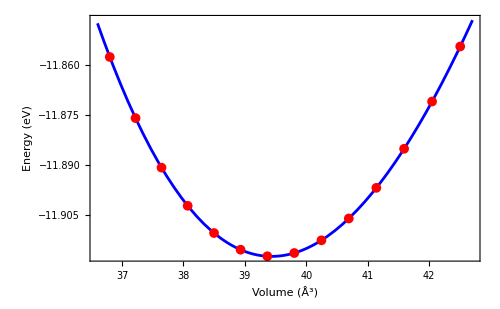

```mathematica
Plot[nlm[v],{v,(cell[[All,1]]//Min)-0.2, (cell[[All,1]]//Max)+0.2},
Frame->True,
FrameLabel->{"Volume (Å^3)", "Energy (eV)"},
PlotStyle->{AbsoluteThickness[2], Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[cell]}]
```

```mathematica
nlm["RSquared"]
```

1.

```mathematica
opvol=FindMinimum[nlm[v],{v,39,40}]
```

{-11.9176,{v→39.4369}}

To get the lattice parameter in this system we have:

```mathematica
Solve[vol == s^3/4,s]
```

{{s→(-2)^(2/3) vol^(1/3)},{s→2^(2/3) vol^(1/3)},{s→-(-1)^(1/3) 2^(2/3) vol^(1/3)}}

```mathematica
2^(2/3) v^(1/3) /.opvol[[2]]
```

5.40324

The bulk modulus B_0 is:

```mathematica
bulkm = v D[nlm[v],{v,2}]/.opvol[[2]]
```

0.602976

```mathematica
UnitConvert[Quantity[bulkm, "Electronvolts"/("Angstroms")^3], "GigaPascals"]
```

96.6073 GPa

```mathematica
-v/bulkm D[v D[nlm//Normal,{v,2}],v]/.opvol[[2]]
```

4.26579

```mathematica
sol=Solve[{
e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],
-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],
63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],
-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlm["BestFitParameters"],{e0,B0,B',v0}]
```

{{e0→-11.9176,B0→0.602976,B'→4.26579,v0→39.4369}}

```mathematica
(vcal-vexp)/vexp 100/.{vexp->5.429,vcal->5.403244142702353}
```

-0.474413

## Part 4 : Functionals

```mathematica
wrk="/home/rolando/Downloads/Yachay/8th\ Semester/dft/hands_on/part4_silicon2";
SetDirectory[wrk];
```

### Results using PBE

```mathematica
cell = Import["cell-pbe.dat"]//Map[{1/4(#[[1]])^3,#[[2]]}&,#]&;
```

```mathematica
cell//TableForm
```

39.366 | -10.8312
39.805 | -10.8397
40.2473 | -10.8452
40.4697 | -10.8469
40.6928 | -10.8478
40.9168 | -10.8481
41.1416 | -10.8477
41.3673 | -10.8466
41.5938 | -10.8448
42.0492 | -10.8394
42.5079 | -10.8315

```mathematica
eos=e0+(9 v0 B0)/16(((v0/v)^(2/3)-1)^3 B0'+((v0/v)^(2/3)-1)^2 (6-4 (v0/v)^(2/3)))
```

e0+9/16 B0 v0 ((6-4 (v0/v)^(2/3)) (-1+(v0/v)^(2/3))^2+(-1+(v0/v)^(2/3))^3 B0')

```mathematica
eos//PowerExpand//ExpandAll//Collect[#,v]&
```

e0+(27 B0 v0)/8-9/16 B0 v0 B0'+(-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B0')/v^(2/3)+(63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B0')/v^(4/3)+(-(9 B0 v0^3)/4+9/16 B0 v0^3 B0')/v^2

```mathematica
model=k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2;
parameters=Table[k[i],{i,4}];
nlm=NonlinearModelFit[cell,model,parameters,v]
```

FittedModel[…]

```mathematica
nlm[v]
```

10.6771+6779.21/v^2+1890.12/v^(4/3)-462.854/v^(2/3)

```mathematica
nlm["BestFitParameters"]
```

{k[1]→10.6771,k[2]→-462.854,k[3]→1890.12,k[4]→6779.21}

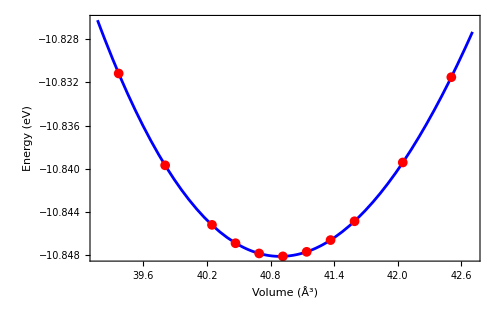

```mathematica
Plot[nlm[v],{v,(cell[[All,1]]//Min)-0.2, (cell[[All,1]]//Max)+0.2},
Frame->True,
FrameLabel->{"Volume (Å^3)", "Energy (eV)"},
PlotStyle->{AbsoluteThickness[2], Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[cell]}]
```

```mathematica
sol=Solve[{
e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],
-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],
63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],
-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlm["BestFitParameters"],{e0,B0,B',v0}]
```

{{e0→-10.8481,B0→0.556041,B'→4.31699,v0→40.8915}}

```mathematica
opvol=FindMinimum[nlm[v],{v,39,40}]
```

{-10.8481,{v→40.8915}}

```mathematica
acal = 2^(2/3) v^(1/3) /.opvol[[2]]
```

5.46887

The error of the predicted lattice parameter is:

```mathematica
(acal-aexpt)/aexpt 100/.{aexpt->5.429}
```

0.734405

The bulk modulus B_0 is:

```mathematica
bulkm = v D[nlm[v],{v,2}]/.opvol[[2]]
```

0.556041

```mathematica
UnitConvert[Quantity[bulkm, "Electronvolts"/("Angstroms")^3], "GigaPascals"]
```

89.0876 GPa

```mathematica
-v/bulkm D[v D[nlm//Normal,{v,2}],v]/.opvol[[2]]
```

4.31699

### Results using PBE-PBEsol

```mathematica
cell = Import["cell-pbesol.dat"]//Map[{1/4(#[[1]])^3,#[[2]]}&,#]&;
```

```mathematica
cell//TableForm
```

36.7995 | -11.3962
37.2192 | -11.42
37.6422 | -11.4402
38.0683 | -11.4569
38.4977 | -11.4702
38.9302 | -11.4802
39.366 | -11.487
39.805 | -11.4908
40.2473 | -11.4917
40.6928 | -11.4897
41.1416 | -11.485
41.5938 | -11.4776
42.0492 | -11.4677
42.5079 | -11.4553

```mathematica
eos=e0+(9 v0 B0)/16(((v0/v)^(2/3)-1)^3 B0'+((v0/v)^(2/3)-1)^2 (6-4 (v0/v)^(2/3)))
```

e0+9/16 B0 v0 ((6-4 (v0/v)^(2/3)) (-1+(v0/v)^(2/3))^2+(-1+(v0/v)^(2/3))^3 B0')

```mathematica
eos//PowerExpand//ExpandAll//Collect[#,v]&
```

e0+(27 B0 v0)/8-9/16 B0 v0 B0'+(-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B0')/v^(2/3)+(63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B0')/v^(4/3)+(-(9 B0 v0^3)/4+9/16 B0 v0^3 B0')/v^2

```mathematica
model=k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2;
parameters=Table[k[i],{i,4}];
nlm=NonlinearModelFit[cell,model,parameters,v]
```

FittedModel[…]

```mathematica
nlm[v]
```

12.1033+4555.29/v^2+2467.84/v^(4/3)-520.264/v^(2/3)

```mathematica
nlm["BestFitParameters"]
```

{k[1]→12.1033,k[2]→-520.264,k[3]→2467.84,k[4]→4555.29}

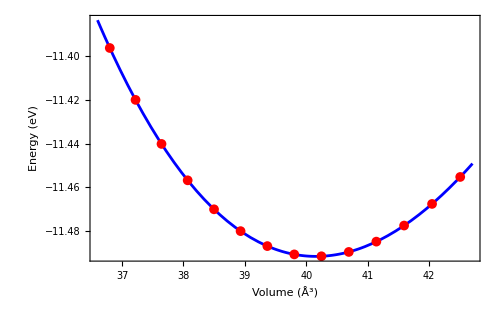

```mathematica
Plot[nlm[v],{v,(cell[[All,1]]//Min)-0.2, (cell[[All,1]]//Max)+0.2},
Frame->True,
FrameLabel->{"Volume (Å^3)", "Energy (eV)"},
PlotStyle->{AbsoluteThickness[2], Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[cell]}]
```

```mathematica
sol=Solve[{
e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],
-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],
63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],
-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlm["BestFitParameters"],{e0,B0,B',v0}]
```

{{e0→-11.4917,B0→0.584801,B'→4.21383,v0→40.1577}}

```mathematica
opvol=FindMinimum[nlm[v],{v,39,40}]
```

{-11.4917,{v→40.1577}}

```mathematica
acal = 2^(2/3) v^(1/3) /.opvol[[2]]
```

5.43596

The error of the predicted lattice parameter is:

```mathematica
(acal-aexpt)/aexpt 100/.{aexpt->5.429}
```

0.12821

The bulk modulus B_0 is:

```mathematica
bulkm = v D[nlm[v],{v,2}]/.opvol[[2]]
```

0.584801

```mathematica
UnitConvert[Quantity[bulkm, "Electronvolts"/("Angstroms")^3], "GigaPascals"]
```

93.6955 GPa

```mathematica
-v/bulkm D[v D[nlm//Normal,{v,2}],v]/.opvol[[2]]
```

4.21384

## Part 5 : The silicon crystal using PBE

```mathematica
wrk = "/home/rolando/Downloads/Yachay/8th Semester/dft/hands_on/part5_silicon3";
SetDirectory[wrk]
```

/home/rolando/Downloads/Yachay/8th Semester/dft/hands_on/part5_silicon3

The cohesion energy in [eV] for Si fcc si predicted to be

```mathematica
e[bulk]/n-e[atom] /.{e[bulk]-> -10.84807047, e[atom]-> -0.88363161, n->2}
```

-4.5404

```mathematica
input=Import["DOSCAR", "Table"];
```

```mathematica
dos=input[[7;;7+300]][[All,{1,2}]];
```

```mathematica
ef=input[[6,4]]
```

5.66955

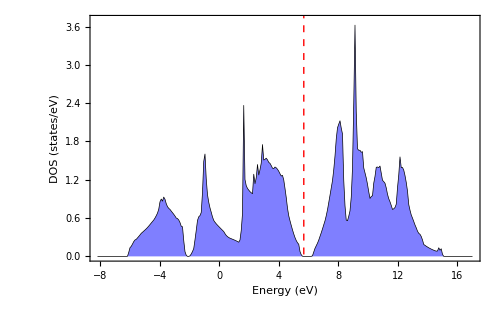

```mathematica
ListPlot[dos,
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)", "DOS (states/eV)"},
GridLines->{{ef}, None},
GridLinesStyle->Directive[Red, Dashed, AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->{All, {0,3.7}}]
```

```mathematica
interp=Interpolation[dos]
```

InterpolatingFunction[…]

```mathematica
NIntegrate[interp[x],{x,-8,ef}]
```

8.05949

Here we are going to analyze de partial density of states (PDOS), the arrange of the data PDOS is according to the AO:
energy,  s,  p_y p_z p_x d_{xy} d_{yz} d_{z2-r2} d_{xz} d_{x2-y2}

```mathematica
dos1=input[[7+300+2;;7+300+2+300]];
dos2=input[[7+300+2+300+2;;7+300+2+300+2+300]];
```

```mathematica
dosall=(dos1+dos2)//Map[#/{2,1,1,1,1,1,1,1,1,1}&,#]&;
```

```mathematica
f[total]=Map[{#[[1]],Plus@@(#[[2;;10]])}&,#]&;
f[s]=Map[{#[[1]],#[[2]]}&,#]&;
f[p]=Map[{#[[1]],Plus@@(#[[3;;5]])}&,#]&;
f[d]=Map[{#[[1]],Plus@@(#[[6;;10]])}&,#]&;
f[py]=Map[{#[[1]],#[[3]]}&,#]&;
f[pz]=Map[{#[[1]],#[[4]]}&,#]&;
f[px]=Map[{#[[1]],#[[5]]}&,#]&;
```

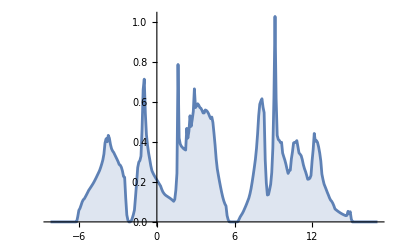

```mathematica
dosall//f[total]//ListPlot[#,Joined->True,Filling->Axis]&
```

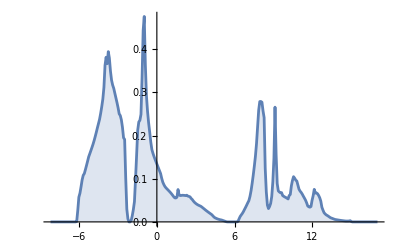

```mathematica
dosall//f[s]//ListPlot[#,Joined->True,Filling->Axis]&
```

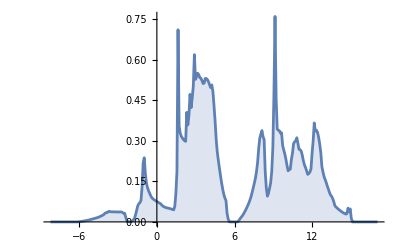

```mathematica
dosall//f[p]//ListPlot[#,Joined->True,Filling->Axis]&
```

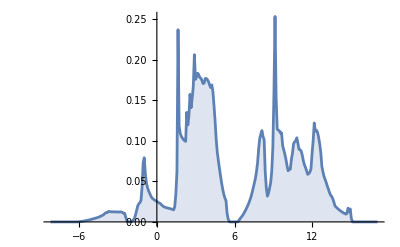

```mathematica
dosall//f[py]//ListPlot[#,Joined->True,Filling->Axis]&
```

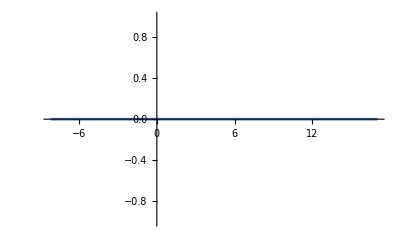

```mathematica
dosall//f[d]//ListPlot[#,Joined->True,Filling->Axis]&
```

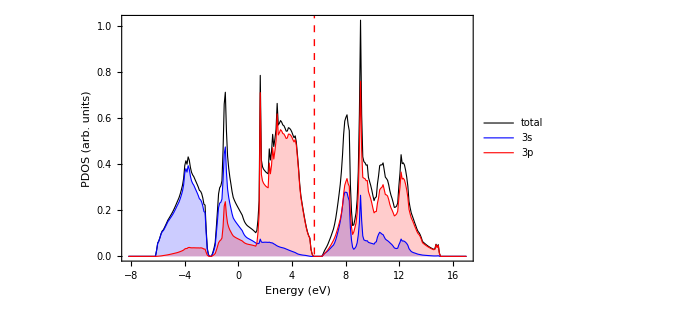

```mathematica
{dosall//f[total],dosall//f[s], dosall//f[p] }//ListPlot[#,
Joined->True,
GridLines->{{ef},None},
Filling->{2->Axis,3->Axis},
Frame->True,
PlotRange->All,
PlotLegends->Placed[{"total", "3s", "3p"}, {Scaled[{0,0.75}],{0,0.5}}],
ImageSize->500,
Axes->None,
GridLinesStyle->Directive[Red, Dashed, AbsoluteThickness[1.0]],
PlotStyle->{{AbsoluteThickness[0.8], Black}, {AbsoluteThickness[0.8], Blue}, {AbsoluteThickness[0.8], Red}},
FrameLabel->{"Energy (eV)", "PDOS (arb. units)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->18}]&
```

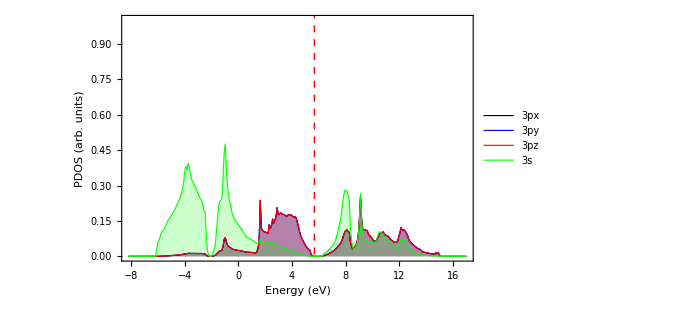

```mathematica
{dosall//f[px],dosall//f[py], dosall//f[pz],dosall//f[s] }//ListPlot[#,
Joined->True,
GridLines->{{ef},None},
Filling->{1->Axis, 2->Axis,3->Axis, 4->Axis},
Frame->True,
PlotRange->{Automatic,{0,1}},
PlotLegends->Placed[{"3px", "3py", "3pz","3s"}, {Scaled[{0,0.75}],{0,0.5}}],
ImageSize->500,
Axes->None,
GridLinesStyle->Directive[Red, Dashed, AbsoluteThickness[1.0]],
PlotStyle->{{AbsoluteThickness[0.8], Black}, {AbsoluteThickness[0.8], Blue}, {AbsoluteThickness[0.8], Red},{AbsoluteThickness[0.8], Green}},
FrameLabel->{"Energy (eV)", "PDOS (arb. units)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->18}]&
```

### Band Structure from PROCAR_OPT Along Path L→Γ→X→K→Γ @Henry Pinto, YTU

The following notebook will allow you to create the band structure from any VASP calculation that produces a PROCAR_OPT file

To run this notebook, be sure you have  in same directory  PROCAR_OPT and KPOINTS_OPT.

%%%% you can run the lines below %%%%%%%%%

```mathematica
Run["grep k-point PROCAR_OPT > kpt"];
Run["sed 's/-/ -/g' kpt > kpt2"];
Run["sed 's/k -point/k-point/g' kpt2 > kpts"];
Run["rm kpt kpt2"];
Run["grep band PROCAR_OPT > bandData"];
Run["grep \"# of bands\" PROCAR_OPT | tail -1 > numbands"];
```

```mathematica
(*define the Fermi elevel take from previous calculations OUTCAR.st*)
ef=input[[6,4]];
```

```mathematica
(*This gets number of kp and bands*)
bandsinfo=Import["numbands","Table"][[1]];
{Nkpt,Nbands}=bandsinfo//{#[[4]],#[[8]]}&
```

{140,8}

```mathematica
(*This gets the high symmetry points and divisions*)
path=Import["KPOINTS-bs","Table"];
div=path[[2,1]];
```

```mathematica
(*This defines the high symmetry points labels and the length*)
hsympts=(If[(path[[5]]//Length)==4,path[[5;;-1]]//Flatten//Partition[#,4]&//#[[All,4]]&, path[[5;;-1]]//Flatten//Partition[#,5]&//#[[All,5]]&]//Drop[#,{3,Length[#],2}]&)/."GAMMA"->"Γ"
NumGridL=(hsympts//Length)-2;
```

{L,Γ,X,K,Γ}

```mathematica
(*This defines the band energies shifted to Ef*)
bands=Import["bandData","Table"][[2;;Nbands Nkpt+1]][[All,5]]-ef//Partition[#,Nbands]&;
bandener=bands//Drop[#,{div,Nkpt-div,div}]&;
```

```mathematica
(*This defines k-point coordinates*)
kp=Import["kpts","Table"][[2;;Nkpt+1]][[All,{4,5,6}]];
kpt=kp//Drop[#,{div,Nkpt-div,div}]&;
```

```mathematica
(*This liniarizes k-point coordinates in 1D*)
kpt2=Join[{0},Table[Norm[kpt[[i+1]]-kpt[[i]]],{i,(kpt//Length)-1}]]//Accumulate;
```

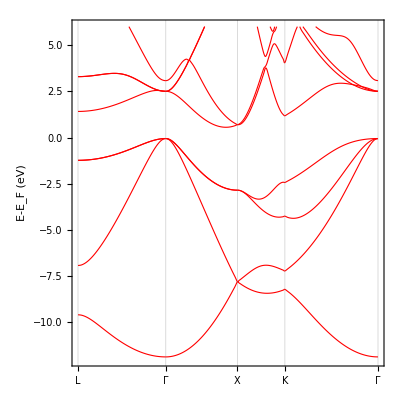

```mathematica
(*This creates the bands in kpt2 domain*)
bands2={kpt2,bandener}//Transpose;
Do[bd[i]=bands2//Map[{#[[1]],#[[2,i]]}&,#]&,{i,Nbands}];

(*please provide the bands you want to plot*)
ListPlot[Table[bd[i],{i,1,8(*Nbands*)}],
Frame->True,
FrameLabel->{"","E-E_F (eV)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->14},
Joined->True,
InterpolationOrder->2,
AspectRatio->1,
AxesStyle->Directive[Black,Dashed, AbsoluteThickness[0.7]],
FrameTicks->{{Automatic,None},{{kpt2[[Join[Table[i div-(i-1),{i,0,NumGridL}],{-1}]]],hsympts}//Transpose,None}},
GridLines->{kpt2[[Join[Table[i div-(i-1),{i,0,NumGridL}],{-1}]]],None},
PlotStyle->Directive[Red,AbsoluteThickness[0.8]],
PlotRange->{{0,kpt2[[-1]]},{-12,6}}]
```

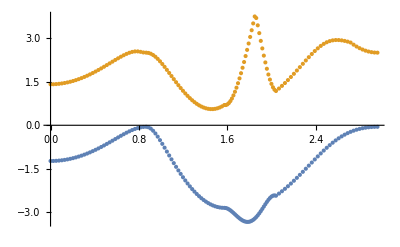

```mathematica
{bd[4],bd[5]}//ListPlot
```

Here we can see the valence band edge and the conductor band edge.

```mathematica
valBand = Interpolation[bd[4]]
```

InterpolatingFunction[…]

```mathematica
condBand = Interpolation[bd[5]]
```

InterpolatingFunction[…]

```mathematica
FindMaximum[valBand[x],{x,0.7}]
```

{-0.0528128,{x→0.860019}}

```mathematica
FindMinimum[condBand[x],{x,1.4}]
```

{0.556632,{x→1.45916}}

```mathematica
bandGap = 0.5566324240957816-(-0.052812811235963375)
```

0.609445

### Visualization of CHGCAR.vasp

In the following image, we display the iso-density of the valence electrons, notice the distribution.

And

## Part 6

```mathematica
wrk = "/home/rolando/Downloads/Yachay/8th Semester/dft/hands_on/part6_silicon4/results";
SetDirectory[wrk];
```

```mathematica
data141 = Import["ecut.dat"]//Map[#/{1,2}&,#]&;
data141//TableForm
```

250 | -5.122
300 | -5.12875
350 | -5.13232
400 | -5.13366
450 | -5.13391
500 | -5.13394
550 | -5.13397
600 | -5.13404
650 | -5.13406
700 | -5.13406
750 | -5.13405
800 | -5.13404
850 | -5.13404
900 | -5.13404

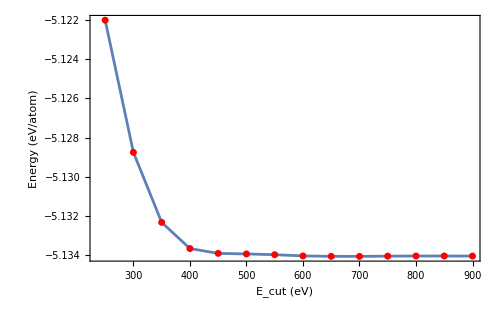

```mathematica
data141//ListPlot[#,
Frame ->True,
FrameLabel->{"E_cut (eV)", "Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->500,
Epilog->{Red, AbsolutePointSize[5], Point[#]}
]&
```

```mathematica
datakp = Import["kps.dat"][[All,{1,2}]]//Map[#/{1,2}&,#]&;
datakp//TableForm
```

0.29531 | -5.1346
0.270177 | -5.13462
0.257611 | -5.13366
0.245044 | -5.13366
0.226195 | -5.13425
0.207345 | -5.13372
0.201062 | -5.13286
0.182212 | -5.13357
0.175929 | -5.13349
0.163363 | -5.13314
0.15708 | -5.13336
0.150796 | -5.13347
0.144513 | -5.13328
0.13823 | -5.13303
0.131947 | -5.13328
0.125664 | -5.13314

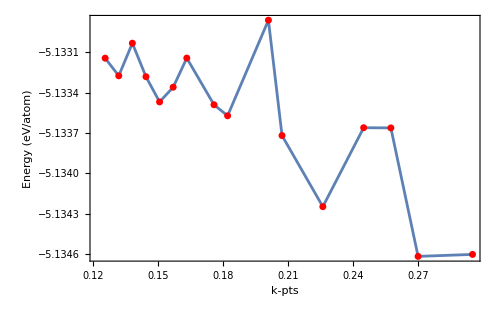

```mathematica
datakp //ListPlot[#,
Frame ->True,
FrameLabel->{"k-pts", "Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->500,
Epilog->{Red, AbsolutePointSize[5], Point[#]}
]&
```

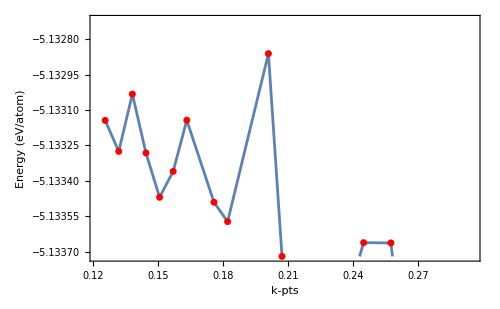

```mathematica
datakp //ListPlot[#,
Frame ->True,
FrameLabel->{"k-pts", "Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->15},
Joined->True,
PlotRange->{#[[6,2]],#[[6,2]]+10^-3},
InterpolationOrder->1,
ImageSize->500,
Epilog->{Red, AbsolutePointSize[5], Point[#]}
]&
```

### The EOS for β-Sn silicon

```mathematica
Import["cell.dat"][[All,{1,2}]]
```

{{27.7,-10.1444},{28.2,-10.1839},{28.7,-10.2148},{29.2,-10.2378},{29.7,-10.2535},{30.2,-10.263},{30.7,-10.2674},{31.2,-10.265},{31.7,-10.2576},{32.2,-10.2456},{32.7,-10.2294},{33.2,-10.2094},{33.7,-10.186},{34.2,-10.1594},{34.7,-10.13}}

```mathematica
cell = Import["cell.dat"][[All,{1,2}]];
```

```mathematica
eos=e0+(9 v0 B0)/16(((v0/v)^(2/3)-1)^3 B0'+((v0/v)^(2/3)-1)^2 (6-4 (v0/v)^(2/3)))
```

e0+9/16 B0 v0 ((6-4 (v0/v)^(2/3)) (-1+(v0/v)^(2/3))^2+(-1+(v0/v)^(2/3))^3 B0')

```mathematica
eos//PowerExpand//ExpandAll//Collect[#,v]&
```

e0+(27 B0 v0)/8-9/16 B0 v0 B0'+(-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B0')/v^(2/3)+(63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B0')/v^(4/3)+(-(9 B0 v0^3)/4+9/16 B0 v0^3 B0')/v^2

```mathematica
model=k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2;
parameters=Table[k[i],{i,4}];
nlm=NonlinearModelFit[cell,model,parameters,v]
```

FittedModel[…]

```mathematica
nlm[v]
```

8.7921+3930.37/v^2+1035.32/v^(4/3)-333.345/v^(2/3)

```mathematica
nlm["BestFitParameters"]
```

{k[1]→8.7921,k[2]→-333.345,k[3]→1035.32,k[4]→3930.37}

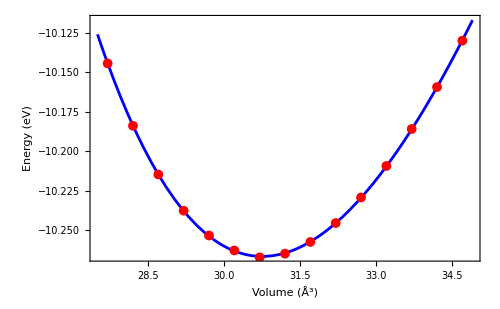

```mathematica
Plot[nlm[v],{v,(cell[[All,1]]//Min)-0.2, (cell[[All,1]]//Max)+0.2},
Frame->True,
FrameLabel->{"Volume (Å^3)", "Energy (eV)"},
PlotStyle->{AbsoluteThickness[2], Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[cell]}]
```

```mathematica
nlm["RSquared"]
```

1.

```mathematica
opvol=FindMinimum[nlm[v],{v,39,40}]
```

{-10.2667,{v→30.7513}}

The bulk modulus B_0 is:

```mathematica
bulkm = v D[nlm[v],{v,2}]/.opvol[[2]]
```

0.671051

```mathematica
UnitConvert[Quantity[bulkm, "Electronvolts"/("Angstroms")^3], "GigaPascals"]
```

107.514 GPa

```mathematica
-v/bulkm D[v D[nlm//Normal,{v,2}],v]/.opvol[[2]]
```

4.35807

```mathematica
sol=Solve[{
e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],
-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],
63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],
-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlm["BestFitParameters"],{e0,B0,B',v0}]
```

{{e0→-10.2667,B0→0.671051,B'→4.35807,v0→30.7513}}

### PDOS

```mathematica
input=Import["DOSCAR-bulk", "Table"];
```

```mathematica
dos=input[[7;;7+300]][[All,{1,2}]];
```

```mathematica
ef=input[[6,4]]
```

9.03194

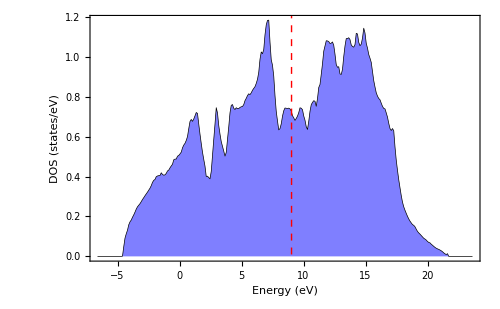

```mathematica
ListPlot[dos,
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)", "DOS (states/eV)"},
GridLines->{{ef}, None},
GridLinesStyle->Directive[Red, Dashed, AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->All]
```

```mathematica
interp=Interpolation[dos]
```

InterpolatingFunction[…]

```mathematica
NIntegrate[interp[x],{x,-8,ef}]
```

InterpolatingFunction::dmvali: The integration endpoint -8 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

7.99965

Here we are going to analyze de partial density of states (PDOS), the arrange of the data PDOS is according to the AO:
energy,  s,  p_y p_z p_x d_{xy} d_{yz} d_{z2-r2} d_{xz} d_{x2-y2}

```mathematica
dos1=input[[7+300+2;;7+300+2+300]];
dos2=input[[7+300+2+300+2;;7+300+2+300+2+300]];
```

```mathematica
dosall=(dos1+dos2)//Map[#/{2,1,1,1,1,1,1,1,1,1}&,#]&;
```

```mathematica
f[total]=Map[{#[[1]],Plus@@(#[[2;;10]])}&,#]&;
f[s]=Map[{#[[1]],#[[2]]}&,#]&;
f[p]=Map[{#[[1]],Plus@@(#[[3;;5]])}&,#]&;
f[d]=Map[{#[[1]],Plus@@(#[[6;;10]])}&,#]&;
f[py]=Map[{#[[1]],#[[3]]}&,#]&;
f[pz]=Map[{#[[1]],#[[4]]}&,#]&;
f[px]=Map[{#[[1]],#[[5]]}&,#]&;
```

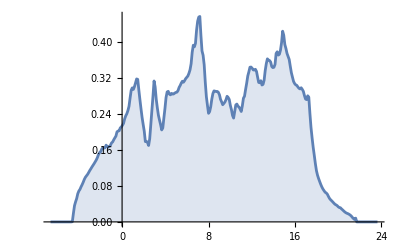

```mathematica
dosall//f[total]//ListPlot[#,Joined->True,Filling->Axis]&
```

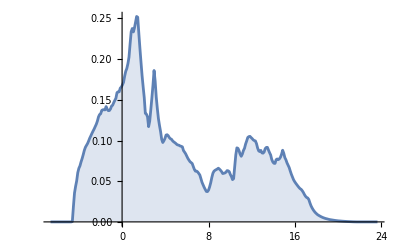

```mathematica
dosall//f[s]//ListPlot[#,Joined->True,Filling->Axis]&
```

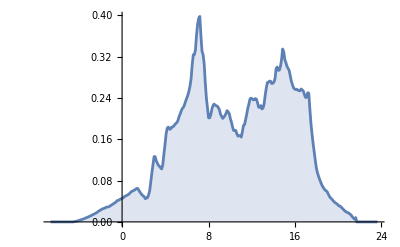

```mathematica
dosall//f[p]//ListPlot[#,Joined->True,Filling->Axis]&
```

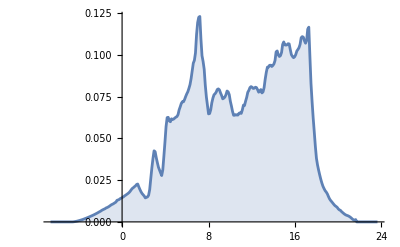

```mathematica
dosall//f[py]//ListPlot[#,Joined->True,Filling->Axis]&
```

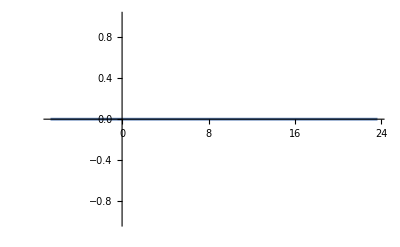

```mathematica
dosall//f[d]//ListPlot[#,Joined->True,Filling->Axis]&
```

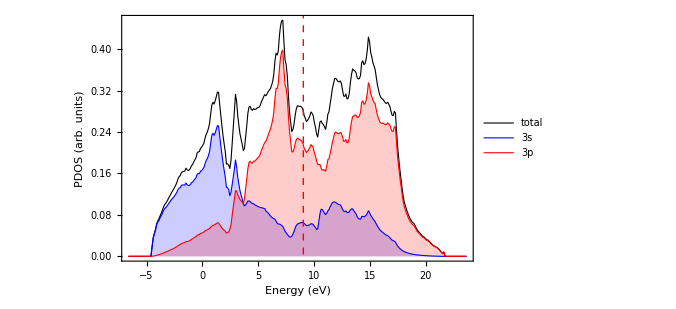

```mathematica
{dosall//f[total],dosall//f[s], dosall//f[p] }//ListPlot[#,
Joined->True,
GridLines->{{ef},None},
Filling->{2->Axis,3->Axis},
Frame->True,
PlotRange->All,
PlotLegends->Placed[{"total", "3s", "3p"}, {Scaled[{0,0.75}],{0,0.5}}],
ImageSize->500,
Axes->None,
GridLinesStyle->Directive[Red, Dashed, AbsoluteThickness[1.0]],
PlotStyle->{{AbsoluteThickness[0.8], Black}, {AbsoluteThickness[0.8], Blue}, {AbsoluteThickness[0.8], Red}},
FrameLabel->{"Energy (eV)", "PDOS (arb. units)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->18}]&
```

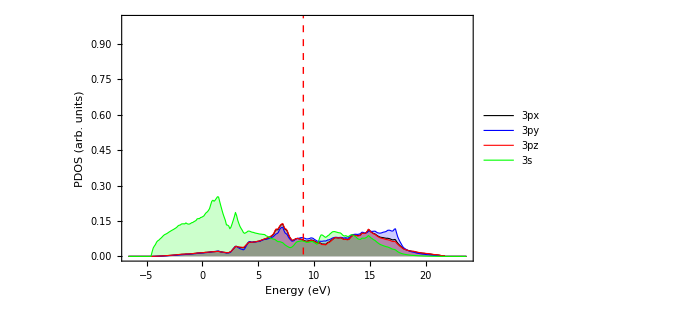

```mathematica
{dosall//f[px],dosall//f[py], dosall//f[pz],dosall//f[s] }//ListPlot[#,
Joined->True,
GridLines->{{ef},None},
Filling->{1->Axis, 2->Axis,3->Axis, 4->Axis},
Frame->True,
PlotRange->{Automatic,{0,1}},
PlotLegends->Placed[{"3px", "3py", "3pz","3s"}, {Scaled[{0,0.75}],{0,0.5}}],
ImageSize->500,
Axes->None,
GridLinesStyle->Directive[Red, Dashed, AbsoluteThickness[1.0]],
PlotStyle->{{AbsoluteThickness[0.8], Black}, {AbsoluteThickness[0.8], Blue}, {AbsoluteThickness[0.8], Red},{AbsoluteThickness[0.8], Green}},
FrameLabel->{"Energy (eV)", "PDOS (arb. units)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->18}]&
```

### Band Structure from PROCAR_OPT Along Path L→Γ→X→K→Γ @Henry Pinto, YTU

The following notebook will allow you to create the band structure from any VASP calculation that produces a PROCAR_OPT file

To run this notebook, be sure you have  in same directory  PROCAR_OPT and KPOINTS_OPT.

%%%% you can run the lines below %%%%%%%%%

```mathematica
Run["grep k-point PROCAR_OPT > kpt"];
Run["sed 's/-/ -/g' kpt > kpt2"];
Run["sed 's/k -point/k-point/g' kpt2 > kpts"];
Run["rm kpt kpt2"];
Run["grep band PROCAR_OPT > bandData"];
Run["grep \"# of bands\" PROCAR_OPT | tail -1 > numbands"];
```

```mathematica
(*define the Fermi elevel take from previous calculations OUTCAR.st*)
ef=input[[6,4]];
```

```mathematica
(*This gets number of kp and bands*)
bandsinfo=Import["numbands","Table"][[1]];
{Nkpt,Nbands}=bandsinfo//{#[[4]],#[[8]]}&
```

{140,8}

```mathematica
(*This gets the high symmetry points and divisions*)
path=Import["KPOINTS-bs","Table"];
div=path[[2,1]];
```

```mathematica
(*This defines the high symmetry points labels and the length*)
hsympts=(If[(path[[5]]//Length)==4,path[[5;;-1]]//Flatten//Partition[#,4]&//#[[All,4]]&, path[[5;;-1]]//Flatten//Partition[#,5]&//#[[All,5]]&]//Drop[#,{3,Length[#],2}]&)/."GAMMA"->"Γ"
NumGridL=(hsympts//Length)-2;
```

{L,Γ,X,K,Γ}

```mathematica
(*This defines the band energies shifted to Ef*)
bands=Import["bandData","Table"][[2;;Nbands Nkpt+1]][[All,5]]-ef//Partition[#,Nbands]&;
bandener=bands//Drop[#,{div,Nkpt-div,div}]&;
```

```mathematica
(*This defines k-point coordinates*)
kp=Import["kpts","Table"][[2;;Nkpt+1]][[All,{4,5,6}]];
kpt=kp//Drop[#,{div,Nkpt-div,div}]&;
```

```mathematica
(*This liniarizes k-point coordinates in 1D*)
kpt2=Join[{0},Table[Norm[kpt[[i+1]]-kpt[[i]]],{i,(kpt//Length)-1}]]//Accumulate;
```

```mathematica
(*This creates the bands in kpt2 domain*)
bands2={kpt2,bandener}//Transpose;
Do[bd[i]=bands2//Map[{#[[1]],#[[2,i]]}&,#]&,{i,Nbands}];

(*please provide the bands you want to plot*)
ListPlot[Table[bd[i],{i,1,8(*Nbands*)}],
Frame->True,
FrameLabel->{"","E-E_F (eV)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->14},
Joined->True,
InterpolationOrder->2,
AspectRatio->1,
AxesStyle->Directive[Black,Dashed, AbsoluteThickness[0.7]],
FrameTicks->{{Automatic,None},{{kpt2[[Join[Table[i div-(i-1),{i,0,NumGridL}],{-1}]]],hsympts}//Transpose,None}},
GridLines->{kpt2[[Join[Table[i div-(i-1),{i,0,NumGridL}],{-1}]]],None},
PlotStyle->Directive[Red,AbsoluteThickness[0.8]],
PlotRange->{{0,kpt2[[-1]]},{-12,6}}]
```

-Graphics-

```mathematica
{bd[4],bd[5]}//ListPlot
```

-Graphics-

Here we can see the valence band edge and the conductor band edge.

```mathematica
valBand = Interpolation[bd[4]]
```

InterpolatingFunction[…]

```mathematica
condBand = Interpolation[bd[5]]
```

InterpolatingFunction[…]

```mathematica
FindMaximum[valBand[x],{x,0.7}]
```

{-0.0528128,{x→0.860019}}

```mathematica
FindMinimum[condBand[x],{x,1.4}]
```

{0.556632,{x→1.45916}}

```mathematica
bandGap = 0.5566324240957816-(-0.052812811235963375)
```

0.609445

### Visualization of CHGCAR.vasp

The cohesion energy for β-Sn Si is predicted to be

```mathematica
e[bulk]/n-e[atom] /.{e[bulk]-> -10.26738149, e[atom]-> -0.88363161, n->2}
```

-4.25006

### Symm 227 (fcc) VS Symm 141

```mathematica
E227=-10.84807047;
```

```mathematica
EOS227[v_]=13.594266553993483+2113.2192245466526/v^2+3088.718244402564/v^(4/3)-565.2716925710312/v^(2/3)-E227
```

24.4423+2113.22/v^2+3088.72/v^(4/3)-565.272/v^(2/3)

```mathematica
EOS141[v_]:=8.792101925111997+3930.367598486751/v^2+1035.31941470454/v^(4/3)-333.3452547582743/v^(2/3)-E227
```

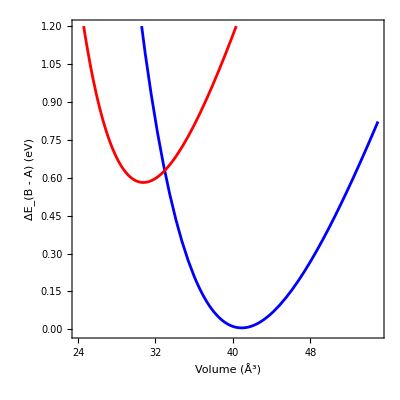

```mathematica
Plot[{EOS227[v],EOS141[v]},{v,24,55},
Frame->True,
FrameLabel->{"Volume (Å^3)","ΔE_(B - A) (eV)"},
PlotRange->{-0.01,1.2},
AspectRatio->1,
PlotStyle->{Blue,Red}]
```

```mathematica
sol=FindRoot[{D[EOS141[v2],v2]==D[EOS227[v1],v1]==(EOS141[v2]-EOS227[v1])/(v2-v1)},{{v1,38},{v2,26}}]
```

{v1→37.3739,v2→28.4833}

```mathematica
(EOS141[v2]-EOS227[v1])/(v2-v1) /.{v1->37.37392931234222,v2->28.483}
```

-0.0607759